```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

Lor1::shdw: Symbol \!\(\*RowBox[{"\"Lor1\""}]\) appears in multiple contexts \!\(\*RowBox[{"{", RowBox[{"\"FormCalc`\"", ",", "\"Global`\""}], "}"}]\); definitions in context \!\(\*RowBox[{"\"FormCalc`\""}]\) may shadow or be shadowed by other definitions.

Lor2::shdw: Symbol \!\(\*RowBox[{"\"Lor2\""}]\) appears in multiple contexts \!\(\*RowBox[{"{", RowBox[{"\"FormCalc`\"", ",", "\"Global`\""}], "}"}]\); definitions in context \!\(\*RowBox[{"\"FormCalc`\""}]\) may shadow or be shadowed by other definitions.

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

SP::shdw: Symbol \!\(\*RowBox[{"\"SP\""}]\) appears in multiple contexts \!\(\*RowBox[{"{", RowBox[{"\"ABISS`\"", ",", "\"Global`\""}], "}"}]\); definitions in context \!\(\*RowBox[{"\"ABISS`\""}]\) may shadow or be shadowed by other definitions.

A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[1]}->{V[2]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/input/kinematics.m already exist. It will NOT be overwritten.

Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "/home/riccardo/Programs/ABISS/models/SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing,NoLightFHCoupling}, ExcludeParticles-> {}];
```

```mathematica
process={V[1]}->{V[2]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/ABISS/models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {/home/riccardo/Programs/ABISS/models/SMbgf_Anglerfish} initialized

Excluding 48 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 15 Particles insertions

Restoring 48 field point(s)

in total: 17 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 15 Particles amplitudes

in total: 17 Particles amplitudes

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

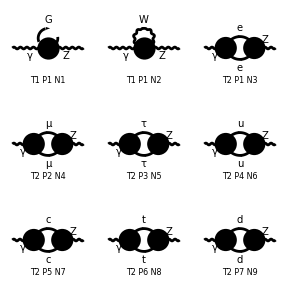

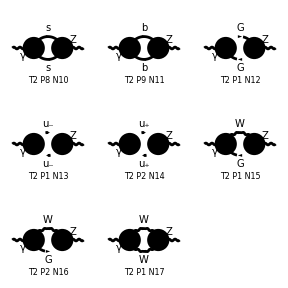

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L]; (*"Extracts from a FeynArts amplitude a list of amplitudes in the format understood by ABISS."*)
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/feynArts_amplitudes/OneLoopAmplitudes.m

```mathematica
FullForm[myAmp1L[[1]]]
```

Times[Complex[0,Rational[1,16]],Power[EL,2],gFFAZ,Power[Pi,-4],FeynAmpDenominator[PropagatorDenominator[FourMomentum[Internal,1],MW]],MetricTensor[Index[Lorentz,1],Index[Lorentz,2]],PolarizationVector[V[1],FourMomentum[Incoming,1],Index[Lorentz,1]],Conjugate[PolarizationVector][V[2],FourMomentum[Outgoing,1],Index[Lorentz,2]]]

## Longitudinal and Transverse Part

### Projectors

```mathematica
l[Lor1_,Lor2_]:=-SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1]
```

```mathematica
t[Lor1_,Lor2_]:=(-SP[{Lor1},{Lor2}]+SP[p1,{Lor1}]SP[p1,{Lor2}]/SP[p1,p1])/(d-1)
```

((SP[p1,{Lor1}] SP[p1,{Lor2}])/SP[p1,p1]-SP[{Lor1},{Lor2}])/(-1+d)

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[1],p_,i_]->1,Conjugate[PolarizationVector][V[2],p_,i_]->1}
```

{ep[V[1],p_,i_]→1,ep^*[V[2],p_,i_]→1}

## Interference

```mathematica
myAmp1LABISS=Map[AmpSquare[#,1]&,myAmp1L];
```

```mathematica
myAmp1LnoEP=myAmp1LABISS/.removePolarizationVectors;
```

```mathematica
myAmp1LLongitudinal=Map[AmpSquare[#*l[Lor1,Lor2],1]&,myAmp1LnoEP];
```

```mathematica
myAmp1LTransverse=Map[AmpSquare[#*t[Lor1,Lor2],1]&,myAmp1LnoEP];
```

```mathematica
SquareSimplifyAndSave[myAmp1LnoEP*l[Lor1,Lor2],{1}]
```

Computed contribution 1-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_1_1.m.

Computed contribution 2-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_2_1.m.

Computed contribution 3-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_3_1.m.

Computed contribution 4-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_4_1.m.

Computed contribution 5-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_5_1.m.

Computed contribution 6-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_6_1.m.

Computed contribution 7-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_7_1.m.

Computed contribution 8-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_8_1.m.

Computed contribution 9-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_9_1.m.

Computed contribution 10-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_10_1.m.

Computed contribution 11-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_11_1.m.

Computed contribution 12-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_12_1.m.

Computed contribution 13-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_13_1.m.

Computed contribution 14-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_14_1.m.

Computed contribution 15-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_15_1.m.

Computed contribution 16-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_16_1.m.

Computed contribution 17-1.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L//interferences/Contribution_17_1.m.

## Shift

```mathematica
ImportInput[];
```

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/input/integral_families.m.

Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,17},{j,1}]
```

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_1_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_2_1.m.

Integral family {A0, {ME}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_3_1.m.

Integral family {A0, {MM}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_4_1.m.

Integral family {A0, {ML}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_5_1.m.

Integral family {A0, {MU}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_6_1.m.

Integral family {A0, {MC}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_7_1.m.

Integral family {A0, {MT}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_8_1.m.

Integral family {A0, {MD}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_9_1.m.

Integral family {A0, {MS}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_10_1.m.

Integral family {A0, {MB}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_11_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_12_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_13_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_14_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_15_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_16_1.m.

Integral family {A0, {MW}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/interferences/Contribution_17_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,17},{j,1}]
```

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_1_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_2_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_3_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_4_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_5_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_6_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_7_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_8_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_9_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_10_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_11_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_12_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_13_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_14_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_15_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_16_1.m.

Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/AZ_L/kira_input/Contribution_17_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},-1,1],userIntegral[A0,{ME},0,0],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,-1],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{MM},-1,1],userIntegral[A0,{MM},0,0],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,-1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{ML},-1,1],userIntegral[A0,{ML},0,0],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,-1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{MU},-1,1],userIntegral[A0,{MU},0,0],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,-1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MC},-1,1],userIntegral[A0,{MC},0,0],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,-1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MT},-1,1],userIntegral[A0,{MT},0,0],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,-1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MD},-1,1],userIntegral[A0,{MD},0,0],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,-1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MS},-1,1],userIntegral[A0,{MS},0,0],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,-1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MB},-1,1],userIntegral[A0,{MB},0,0],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,-1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MW},-1,1],userIntegral[A0,{MW},0,0],userIntegral[A0,{MW},0,1],userIntegral[A0,{MW},1,-1],userIntegral[A0,{MW},1,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[A0,{m1},0,0]→0,userIntegral[A0,{m1},-1,1]→psq userIntegral[A0,{m1},1,0],userIntegral[A0,{m1},0,1]→userIntegral[A0,{m1},1,0],userIntegral[A0,{m1},1,-1]→psq userIntegral[A0,{m1},1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},-1,1],userIntegral[A0,{ME},0,0],userIntegral[A0,{ME},0,1],userIntegral[A0,{ME},1,-1],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{MM},-1,1],userIntegral[A0,{MM},0,0],userIntegral[A0,{MM},0,1],userIntegral[A0,{MM},1,-1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{ML},-1,1],userIntegral[A0,{ML},0,0],userIntegral[A0,{ML},0,1],userIntegral[A0,{ML},1,-1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{MU},-1,1],userIntegral[A0,{MU},0,0],userIntegral[A0,{MU},0,1],userIntegral[A0,{MU},1,-1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MC},-1,1],userIntegral[A0,{MC},0,0],userIntegral[A0,{MC},0,1],userIntegral[A0,{MC},1,-1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MT},-1,1],userIntegral[A0,{MT},0,0],userIntegral[A0,{MT},0,1],userIntegral[A0,{MT},1,-1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MD},-1,1],userIntegral[A0,{MD},0,0],userIntegral[A0,{MD},0,1],userIntegral[A0,{MD},1,-1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MS},-1,1],userIntegral[A0,{MS},0,0],userIntegral[A0,{MS},0,1],userIntegral[A0,{MS},1,-1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MB},-1,1],userIntegral[A0,{MB},0,0],userIntegral[A0,{MB},0,1],userIntegral[A0,{MB},1,-1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MW},-1,1],userIntegral[A0,{MW},0,0],userIntegral[A0,{MW},0,1],userIntegral[A0,{MW},1,-1],userIntegral[A0,{MW},1,1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[A0,{MW},1,0],userIntegral[A0,{ME},1,0],userIntegral[A0,{ME},1,1],userIntegral[A0,{MM},1,0],userIntegral[A0,{MM},1,1],userIntegral[A0,{ML},1,0],userIntegral[A0,{ML},1,1],userIntegral[A0,{MU},1,0],userIntegral[A0,{MU},1,1],userIntegral[A0,{MC},1,0],userIntegral[A0,{MC},1,1],userIntegral[A0,{MT},1,0],userIntegral[A0,{MT},1,1],userIntegral[A0,{MD},1,0],userIntegral[A0,{MD},1,1],userIntegral[A0,{MS},1,0],userIntegral[A0,{MS},1,1],userIntegral[A0,{MB},1,0],userIntegral[A0,{MB},1,1],userIntegral[A0,{MW},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,17},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"RESULTS/Coefficients_"<>ToString[i]<>"_1.m")],{i,17}]
```

```mathematica
diagramCoefficients
```

{{-(ⅈ EL^2 gFFAZ)/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{(ⅈ (-1+d) EL^2 gWWAZ)/(8 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),0},{-(ⅈ EL^2 gFFA gFFZ psq)/(8 pasq π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gFFA gFFZ (pasq-pzsq)^2)/(64 pasq π^4)},{(ⅈ EL^2 ggmgmA ggmgmZ psq)/(32 pasq π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggmgmA ggmgmZ pzsq)/(64 π^4)},{(ⅈ EL^2 ggpgpA ggpgpZ psq)/(32 pasq π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 ggpgpA ggpgpZ pzsq)/(64 π^4)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gFAW gFZW SW)/(16 π^4)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(ⅈ EL^2 gFAW gFZW SW)/(16 π^4)},{-(ⅈ (-3+2 d) EL^2 gWWA gWWZ psq)/(16 pasq π^4)+(ⅈ EL^2 gWWA gWWZ ((-5+2 d) pasq+(3-2 d) pzsq))/(32 pasq π^4)-(ⅈ EL^2 gWWA gWWZ ((-1+2 d) pasq+(3-2 d) pzsq))/(32 pasq π^4),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 gWWA gWWZ (8 MW^2 pasq+(-7+d) pasq^2-2 (-4+d) pasq pzsq+(-3+d) pzsq^2))/(64 pasq π^4)}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{-(ⅈ EL^2 gFFAZ)/(16 π^4)+(ⅈ (-1+d) EL^2 gWWAZ)/(8 π^4)-(ⅈ EL^2 gFFA gFFZ psq)/(8 pasq π^4)+(ⅈ EL^2 ggmgmA ggmgmZ psq)/(32 pasq π^4)+(ⅈ EL^2 ggpgpA ggpgpZ psq)/(32 pasq π^4)-(ⅈ (-3+2 d) EL^2 gWWA gWWZ psq)/(16 pasq π^4)+(ⅈ EL^2 gWWA gWWZ ((-5+2 d) pasq+(3-2 d) pzsq))/(32 pasq π^4)-(ⅈ EL^2 gWWA gWWZ ((-1+2 d) pasq+(3-2 d) pzsq))/(32 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) psq)/(8 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) (2 pasq-pzsq))/(16 pasq π^4)+(ⅈ EL^2 gAl (gZlL+gZlR) pzsq)/(16 pasq π^4),-(ⅈ EL^2 gAl (gZlL+gZlR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAu (gZuL+gZuR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAu (gZuL+gZuR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) psq)/(8 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) (2 pasq-pzsq))/(16 pasq π^4)+(3 ⅈ EL^2 gAd (gZdL+gZdR) pzsq)/(16 pasq π^4),-(3 ⅈ EL^2 gAd (gZdL+gZdR) (pasq-pzsq))/(16 π^4),-(ⅈ EL^2 gFFA gFFZ (pasq-pzsq)^2)/(64 pasq π^4)-(ⅈ EL^2 ggmgmA ggmgmZ pzsq)/(64 π^4)-(ⅈ EL^2 ggpgpA ggpgpZ pzsq)/(64 π^4)-(ⅈ EL^2 gWWA gWWZ (8 MW^2 pasq+(-7+d) pasq^2-2 (-4+d) pasq pzsq+(-3+d) pzsq^2))/(64 pasq π^4)+(ⅈ EL^2 gFAW gFZW SW)/(8 π^4)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
```

```mathematica
parameterReplace=smparameters
```

{gZlL→(-1/2+SW^2)/(CW SW),gZlR→SW/CW,gZNL→1/(2 CW SW),gZuL→(1/2-(2 SW^2)/3)/(CW SW),gZuR→-(2 SW)/(3 CW),gZdL→(-1/2+SW^2/3)/(CW SW),gZdR→SW/(3 CW),gAl→1,gAu→-2/3,gAd→1/3,gWNl→1/(√2 SW),gWlN→1/(√2 SW),gWud→1/(√2 SW),gWdu→1/(√2 SW),gWWZ→CW/SW,gWWA→1,gWWWW→1/SW^2,gWWZZ→-CW^2/SW^2,gWWAZ→CW/SW,gWWAA→-1,gHHHH→-3/(4 MW^2 SW^2),gXXXX→-3/(4 MW^2 SW^2),gHHXX→1/(2 SW^2),gHHFF→1/(2 SW^2),gXXFF→1/(2 SW^2),gFFFF→1/(2 SW^2),gHXFF→1/(4 CW^2),gHHH→-3/(2 MW SW),gHXX→-1/(2 MW SW),gHFF→-1/(2 MW SW),gXFF→(MW SW)/(2 CW^2),gHHZZ→1/(2 CW^2 SW^2),gXXZZ→1/(2 CW^2 SW^2),gHHWW→1/(2 SW^2),gXXWW→1/(2 SW^2),gFFWW→1/(2 SW^2),gFFAA→2,gFFAZ→(-CW^2+SW^2)/(CW SW),gFFZZ→((-CW^2+SW^2)^2)/(2 CW^2 SW^2),gHFAW→-1/(2 SW),gHFZW→-1/(2 CW),gXFAW→1/(2 SW),gHFZW→-1/(2 CW),gXFZW→1/(2 CW),gHXWW→1/(2 SW^2),gHXZ→1/(2 CW SW),gFFA→1,gFFZ→(CW^2-SW^2)/(2 CW SW),gHFW→1/(2 SW),gXFW→1/(2 SW),gHZZ→MW/(CW^2 SW),gHWW→MW/SW,gXWW→MW/SW,gFAW→-MW,gFZW→MW/CW,gHll→-1/(2 MW SW),gHuu→-1/(2 MW SW),gHdd→-1/(2 MW SW),gXll→1/(2 MW SW),gXuu→1/(2 MW SW),gXdd→1/(2 MW SW),gFll→1/(√2 MW SW),gFud→1/(√2 MW SW),gFdu→1/(√2 MW SW),ggpgpA→1,ggmgmA→1,ggpgpZ→CW/SW,ggmgmZ→CW/SW,ggzgpW→CW/SW,ggzgmW→CW/SW,ggagpW→1,ggagmW→1,gHgzgz→-MW/(CW^2 SW),gHgpgp→-MW/SW,gHgmgm→-MW/SW,gXgpgp→MW/(2 SW),gXgmgm→MW/(2 SW),gFgzgp→MW/CW,gFgzgm→MW/CW,gFgagm→MW,gFgagp→MW,ggpgpAA→1,ggmgmAA→1,ggpgpAZ→-CW/SW,ggmgmAZ→-CW/SW,ggpgpZZ→CW^2/SW^2,ggmgmZZ→CW^2/SW^2,ggagpAW→-1,ggagmAW→-1,ggagpZW→CW/SW,ggagmZW→CW/SW,ggzgpAW→CW/SW,ggzgmAW→CW/SW,ggzgpZW→-CW^2/SW^2,ggzgmZW→-CW^2/SW^2,ggagaWW→1,ggagzWW→-CW/SW,ggzgzWW→CW^2/SW^2,ggpgpWW→1/SW^2,ggmgmWW→1/SW^2,ggpgmWW→-1/SW^2,gHHgzgz→-1/(2 CW^2 SW^2),gHHgpgp→-1/(2 SW^2),gHHgmgm→-1/(2 SW^2),gXXgzgz→-1/(2 CW^2 SW^2),gXXgpgp→-1/(2 SW^2),gXXgmgm→-1/(2 SW^2),gFFgaga→-1,gFFgzgz→((CW^2-SW^2)^2)/(2 CW^2 SW^2),gFFgpgp→-1/(2 SW^2),gFFgmgm→-1/(2 SW^2),gFFgagz→(CW^2-SW^2)/(CW SW),gHXgpgp→1/(4 SW^2),gHXgmgm→1/(4 SW^2),gHFgagp→1/(2 SW),gHFgagm→1/(2 SW),gHFgzgp→1/(2 CW),gHFgzgm→1/(2 CW),gXFgagp→1/(2 SW),gXFgagm→1/(2 SW),gXFgzgp→1/(2 CW),gXFgzgm→1/(2 CW)}

```mathematica
coefficients/.parameterReplace/.{pasq->psq,pzsq->psq}//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 MW^2 (CW^2+SW^2))/(8 CW π^4 SW)}

```mathematica
coefficients/.{pasq->psq,pzsq->psq}//Simplify
```

{-1/(32 π^4)ⅈ EL^2 (2 gFFAZ+4 gFFA gFFZ-ggmgmA ggmgmZ-ggpgpA ggpgpZ+4 gWWAZ-4 d gWWAZ-2 gWWA gWWZ+4 d gWWA gWWZ),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 (gWWA gWWZ (8 MW^2-2 psq)+ggmgmA ggmgmZ psq+ggpgpA ggpgpZ psq-8 gFAW gFZW SW))/(64 π^4)}

```mathematica
%/.parameterReplace//Simplify
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(ⅈ EL^2 MW^2 (CW^2+SW^2))/(8 CW π^4 SW)}